```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/standard_model_bbn

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = Map[Read[StringToStream[#],Number]&, linesEl, {2}];
```

```mathematica
T= Last[linesEl][[1]];
distEl1=Last[linesEl][[2;;]];
yEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesEl[[1]]][[3;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

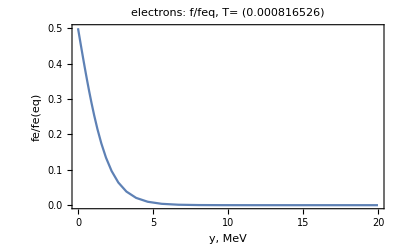

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electrons: f/feq, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fe/fe(eq)"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ = Map[Read[StringToStream[#],Number]&, linesμ, {2}];
```

```mathematica
Tμ= Last[linesμ][[1]];
distμ=Last[linesμ][[2;;]];
yμ=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesμ[[1]]][[3;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

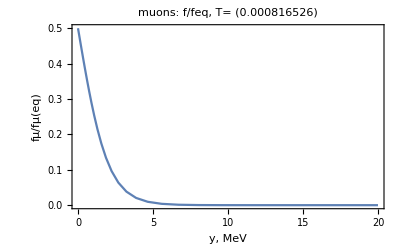

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons: f/feq, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fμ/fμ(eq)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
finalplotfEl=Interpolation[multiplier/@plotDataEl];
finalplotfμ=Interpolation[multiplier/@plotDataμ];
```

```mathematica
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
```

```mathematica
finalspectraSMTest=Import["../../figures/Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
```

```mathematica
finalnueSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,8}]]];
```

```mathematica
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
```

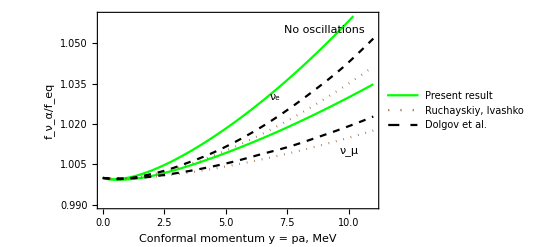

```mathematica
plt=Plot[{
finalplotfEl[y],
finalplotfμ[y],
finalnueSMTestFunc[y],
finalnumuSMTestFunc[y],
finalspectranueSMDigitFunc[y],
finalspectranumuSMDigitFunc[y]
},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown,Dotted},{Brown,Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Dolgov et al.",None}]
Export["Figures-sources/final-spectra-SM-noosc.eps",%];
```